## Data Imports & Definitions:

```mathematica
(*directory string is where the Data folder is stored on your PC*)
dirstring="C:\\Users\\Mason\\OneDrive\\Documents\\PY 452 - Advanced Lab\\Final Project\\";
data1 = Import[dirstring<>"Data\\given\\0.5_data.csv"];
data2 = Import[dirstring<>"Data\\given\\1_data.csv"];
data3 = Import[dirstring<>"Data\\given\\2_data.csv"];
data4 = Import[dirstring<>"Data\\given\\4_data.csv"];
data5 = Import[dirstring<>"Data\\given\\6_data.csv"];
g[λ_,μ_,s1_,s2_]:=Quiet[Piecewise[{{Exp[-1/2(λ-μ)^2/s1^2],λ<μ},{Exp[-1/2(λ-μ)^2/s2^2],λ≥ μ}}]];
xbar[λ_]:=Quiet[1.056*g[λ,599.8,37.9,31.0] + 0.362*g[λ,442.0,16.0,26.7] - 0.065*g[λ,501.1,20.4,26.2]];ybar[λ_]:=Quiet[0.821*g[λ,568.8,46.9,40.5]+0.286*g[λ,530.9,16.3,31.1]];
zbar[λ_]:=Quiet[1.217*g[λ,437.0,11.8,36.0] + 0.681*g[λ,459.0,26.0,13.8]];
```

```mathematica
CIEx=Plot[xbar[x],{x,300,800},PlotStyle->{{Red,Dashed}},PlotLegends->{"CIE Red"}];
CIEy=Plot[ybar[x],{x,300,800},PlotStyle->{{Green,Dashed}},PlotLegends->{"CIE Green"}];
CIEz=Plot[zbar[x],{x,300,800},PlotStyle->{{Blue,Dashed}},PlotLegends->{"CIE Blue"},PlotRange->{{300,800},{0,2}}];
Show[CIEx,CIEy,CIEz,PlotRange->{{300,800},{0,2}}]
```

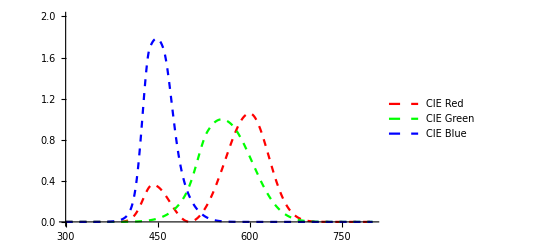

```mathematica
Paraplot=ParametricPlot[{xbar[λ]/(xbar[λ]+ybar[λ]+zbar[λ]),ybar[λ]/(xbar[λ]+ybar[λ]+zbar[λ])},{λ,440,720}, PlotStyle->{Black}];
purewave = ParallelTable[{xbar[i]/(xbar[i]+ybar[i]+zbar[i]),ybar[i]/(xbar[i]+ybar[i]+zbar[i])},{i,440,720,0.1}];

pureslope = (purewave[[2042,2]]-purewave[[1,2]])/(purewave[[2042,1]]-purewave[[1,1]]);
pureint =purewave[[1,2]]-(pureslope*purewave[[1,1]]);
purexpoints = Subdivide[purewave[[1,1]],purewave[[2042,1]],1000];
pureypoints =purexpoints[[;;]]*pureslope+pureint;
pureline = Transpose[{purexpoints, pureypoints}];
pureborder =Join[pureline,purewave];
purearea = Area[ConvexHullMesh[pureborder]];
```

## Module Definitions:

colorcoords:

```mathematica
colorcords[datapoints_]:=
Module[{data = datapoints, len, xchrome, xbardata,ybardata, zbardata, Xcap, Ycap, Zcap, ychrome, cords, dt},
len = Length[data[[;;,1]]];
dt = data[[2,1]]  - data[[3,1]];
cords = {};

xbardata = ParallelTable[xbar[data[[i,1]]],{i,1,len}];
ybardata = ParallelTable[ybar[data[[i,1]]],{i,1,len}];
zbardata = ParallelTable[zbar[data[[i,1]]],{i,1,len}];

Xcap = Total[data[[;;,2]]*xbardata[[;;]]*dt];
Ycap = Total[data[[;;,2]]*ybardata[[;;]]*dt];
Zcap = Total[data[[;;,2]]*zbardata[[;;]]*dt];

xchrome = Xcap/(Xcap+Ycap+Zcap);
ychrome = Ycap/(Xcap+Ycap+Zcap);

cords = Append[cords, xchrome];
cords = Append[cords, ychrome];
cords
]
```

purity :

```mathematica
purity[coordinates_]:=
Module[{data= coordinates, len, slope, int, yw,xw,xpoints,xplointsl,ypoints,points,nearest,distance,closeidx, purity,distanceclosest, xdistancepure, ydistancepure, xdistancetrue, ydistancetrue, endpoint,plotu},

len =1000;
xw = 0.34567;
yw = 0.3585;

slope = (data[[2]] - yw)/(data[[1]] - xw);
int = data[[2]] - (slope*data[[1]]);

If [data[[1]]<xw &&data[[2]]<yw,endpoint=xw,endpoint=1.0];
xpoints=Subdivide[0.0,endpoint,len];
ypoints = xpoints[[;;]]*slope + int;

points = Transpose[{xpoints, ypoints}];

nearest = Nearest[purewave, points[[;;]]];
distanceclosest = Sqrt[(points[[;;,1]]-nearest[[;;,1,1]])^2 + (points[[;;,2]] - nearest[[;;,1,2]])^2];
closeidx = Position[distanceclosest, Min[distanceclosest]];

xdistancepure = points[[closeidx[[1]]]][[1,1]]-xw;
ydistancepure = points[[closeidx[[1]]]][[1,2]]-yw;
xdistancetrue = data[[1]]-xw;
ydistancetrue =data[[2]]-yw;

purity = (Abs[xdistancetrue]+Abs[ydistancetrue])/(Abs[xdistancepure]+Abs[ydistancepure]);
purity
]
```

normalize :

```mathematica
normalize[coordinates_]:=
Module[{data= coordinates,int},
int =Integrate[Interpolation[data,InterpolationOrder->3][x],{x,Min[300],Max[800]}];
data[[;;,2]] = data[[;;,2]]/Abs[int];
If[data[[;;,2]]<0,{data[[;;,2]]=0},{data[[;;,2]]}];
data
]
```

dataout :

```mathematica
dataout[redData_,blueData_, greenData_,backData_]:=
Module[{Rdata = redData, Bdata= blueData,Gdata=greenData,back=backData, Rplot,Bplot,Gplot,area,triarea,
Rcords, Bcords, Gcords, Rpurity, Bpurity, Gpurity, labelr, labelb, labelg, dataplot,dataplotfinal,triangle,
tricover,triplot, labelarea},
Rdata[[;;,2]]=Rdata[[;;,2]]-back[[;;,2]];
Bdata[[;;,2]]=Bdata[[;;,2]]-back[[;;,2]];
Gdata[[;;,2]]=Gdata[[;;,2]]-back[[;;,2]];

Rdata=normalize[Rdata];
Gdata=normalize[Gdata];
Bdata=normalize[Bdata];

Rcords = colorcords[Rdata];
Bcords = colorcords[Bdata];
Gcords = colorcords[Gdata];

triangle = ConvexHullMesh[{Rcords,Bcords,Gcords}];
triarea =Area[triangle];

tricover = PercentForm[Round[triarea/purearea,0.0001]];

Rpurity = purity[Rcords];
Bpurity = purity[Bcords];
Gpurity = purity[Gcords];

labelr = Text[Round[Rpurity,0.001],{Rcords[[1]],Rcords[[2]]+0.03}];
labelb = Text[Round[Bpurity,0.001],{Bcords[[1]],Bcords[[2]]+0.03}];
labelg = Text[Round[Gpurity,0.001],{Gcords[[1]],Gcords[[2]]+0.03}];
labelarea = Text[tricover, {0.34567,0.3585}];

Rplot = ListLinePlot[{Rdata}, PlotRange ->{{300,800},All}, PlotStyle->{Red}];
Bplot = ListLinePlot[{Bdata}, PlotRange->{{300, 800}, All},PlotStyle->{Blue}];
Gplot =  ListLinePlot[{Gdata}, PlotRange ->{{300,800},All}, PlotStyle->{Green}];

triplot = RegionPlot[triangle, BoundaryStyle->{Black,Dashed, Opacity[0.5]}, PlotStyle->{Black,Opacity[0.1]}];

dataplot = ListPlot[{Rcords,Bcords,Gcords}, PlotRange->{{0,1},{0,1}},PlotStyle->{Black}];
dataplotfinal =Show[ChromaticityPlot[Appearance->{"FilledVisibleSpectrum","Wavelengths"->True}],triplot,dataplot,Graphics[{Black,{labelr, labelb,labelg,labelarea}}]];
CellPrint@ExpressionCell[#,"Output"]&/@{Rplot,Bplot,Gplot,dataplotfinal};
]
```

## Testing Modules :

```mathematica
cords1 = colorcords[data1];
cords2 = colorcords[data2];
cords3 = colorcords[data3];
cords4 = colorcords[data4];
cords5 = colorcords[data5];
cordplot = ListPlot[{{0.4,0.2},cords3,cords4,cords5}, PlotRange ->{{0,1},{0,1}}, PlotStyle->{Black}];
```

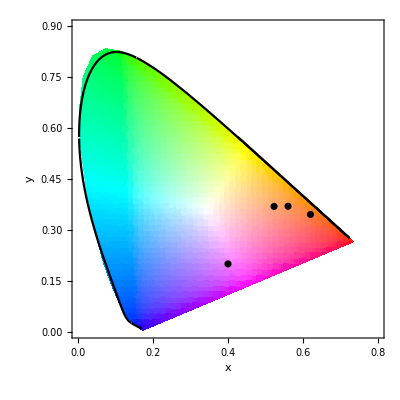

```mathematica
Show[ChromaticityPlot[],cordplot,Paraplot]
```

```mathematica
purity1 = purity[cords1];
purity2 = purity[cords2];
purity3 = purity[cords3];
purity4 = purity[cords4];
purity5 = purity[cords5];
```

```mathematica
gp2Red   = Import[dirstring<>"Data\\gp2\\gp2_red.csv"];
gp2Blue = Import[dirstring<>"Data\\gp2\\gp2_blue.csv"];
gp2Green= Import[dirstring<>"Data\\gp2\\gp2_green.csv"];
gp2Back  = Import[dirstring<>"Data\\gp2\\gp2_back.csv"];

CIEgreen = Table[ybar[i],{i,300,800}];
CIEblue   = Table[zbar[i], {i,300,800}];
CIEred     = Table[xbar[i], {i,300, 800}];
CIExvals = Table[i,{i,300,800}];

CIEgreen=Transpose@{CIExvals,CIEgreen};
CIEblue = Transpose@{CIExvals, CIEblue};
CIEred = Transpose@{CIExvals, CIEred};

CIEgreen = normalize[CIEgreen];
CIEblue = normalize[CIEblue];
CIEred = normalize[CIEred];

CIEredNormalized= ListLinePlot[{CIEred},PlotRange->{{300,800},{0,1.1}}, PlotStyle->{{Red,Dashed}}];
CIEblueNormalized= ListLinePlot[{CIEblue},PlotRange->{{300,800},{0,1.1}}, PlotStyle->{{Blue,Dashed}}];
CIEgreenNormalized= ListLinePlot[{CIEgreen},PlotRange->{{300,800},{0,1.1}}, PlotStyle->{{Green,Dashed}}];
```

## IPhone X_R:

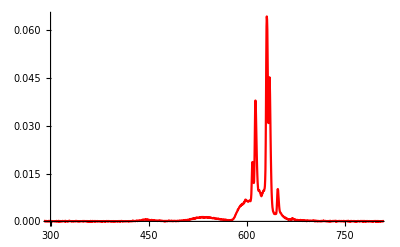

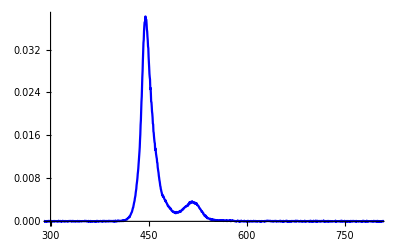

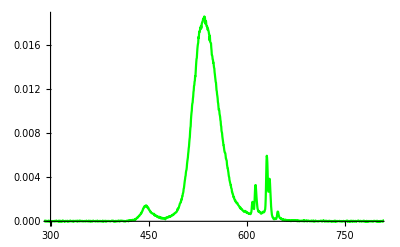

```mathematica
ipxrRed   = Import[dirstring<>"Data\\ipxr\\ipxr_red.csv"];
ipxrBlue = Import[dirstring<>"Data\\ipxr\\ipxr_blue.csv"];
ipxrGreen= Import[dirstring<>"Data\\ipxr\\ipxr_green.csv"];
ipxrBack  = Import[dirstring<>"Data\\ipxr\\ipxr_back.csv"];
dataout[ipxrRed, ipxrBlue, ipxrGreen, ipxrBack]
```

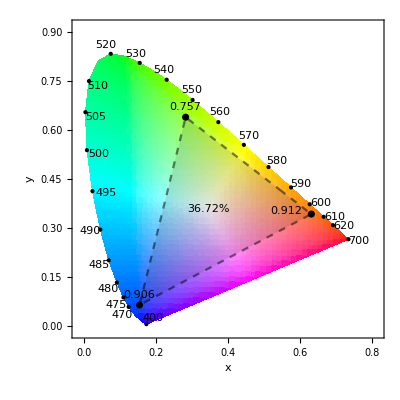

## Google Pixel 4:

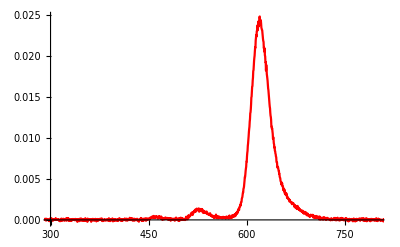

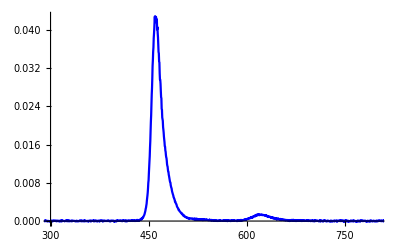

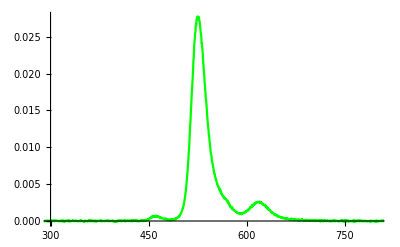

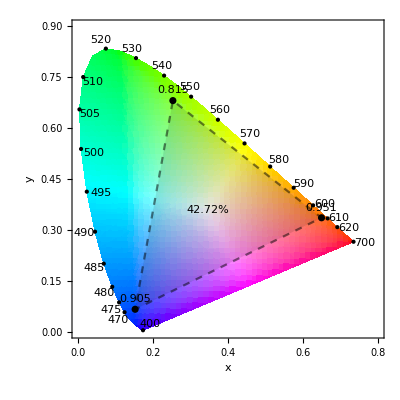

```mathematica
gp4Red   = Import[dirstring<>"Data\\gp4\\gp4_red.csv"];
gp4Blue =Import[dirstring<>"Data\\gp4\\gp4_blue.csv"];
gp4Green= Import[dirstring<>"Data\\gp4\\gp4_green.csv"];
gp4Back  = Import[dirstring<>"Data\\gp4\\gp4_back.csv"];
dataout[gp4Red, gp4Blue, gp4Green, gp4Back]
```

## Nintendo 3 DS :

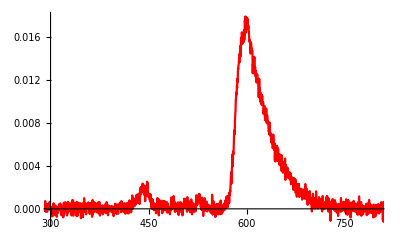

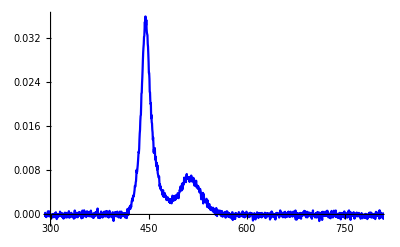

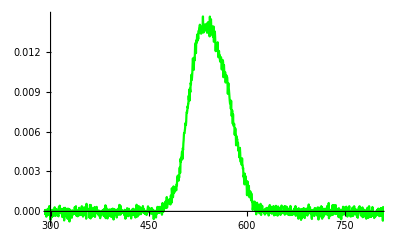

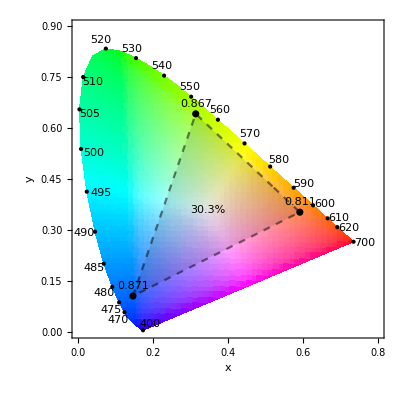

```mathematica
dsRed   = Import[dirstring<>"Data\\3ds\\3ds_red.csv"];
dsBlue = Import[dirstring<>"Data\\3ds\\3ds_blue.csv"];
dsGreen= Import[dirstring<>"Data\\3ds\\3ds_green.csv"];
dsBack  = Import[dirstring<>"Data\\3ds\\3ds_back.csv"];
dataout[dsRed, dsBlue, dsGreen, dsBack]
```

## Nintendo Switch:

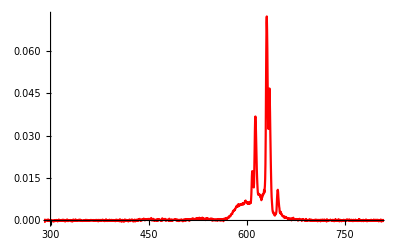

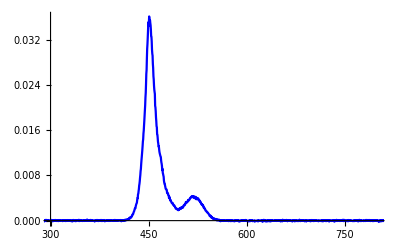

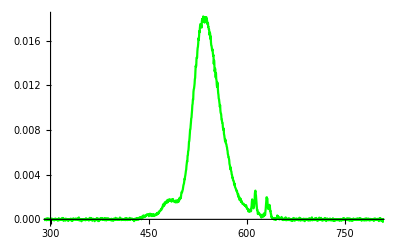

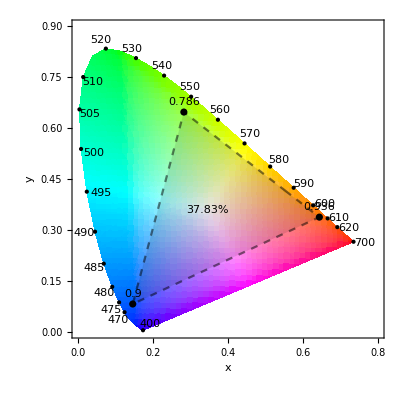

```mathematica
switchRed   = Import[dirstring<>"Data\\switch\\switch_red.csv"];switchBlue = Import[dirstring<>"Data\\switch\\switch_blue.csv"];
switchGreen= Import[dirstring<>"Data\\switch\\switch_green.csv"];
switchBack  = Import[dirstring<>"Data\\switch\\switch_back.csv"];
dataout[switchRed, switchBlue, switchGreen, switchBack]
```

## IPhone 5 :

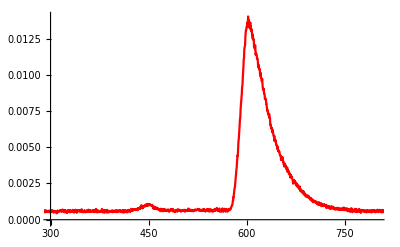

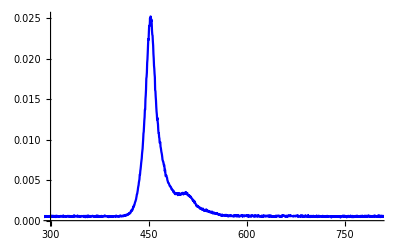

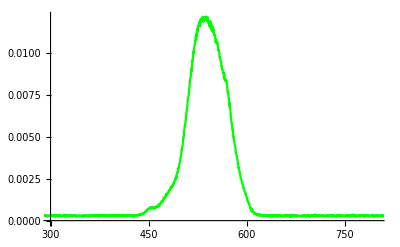

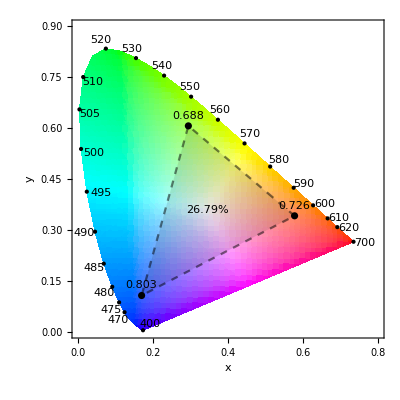

```mathematica
ip5Red  = Import[dirstring<>"Data\\ip5\\ip5_red.csv"];
ip5Blue = Import[dirstring<>"Data\\ip5\\ip5_blue.csv"];
ip5Green= Import[dirstring<>"Data\\ip5\\ip5_green.csv"];

ip5Red= normalize[ip5Red];
ip5Green=normalize[ip5Green];
ip5Blue=normalize[ip5Blue];

ip5Redcord= colorcords[ip5Red];
ip5Bluecord = colorcords[ip5Blue];
ip5Greencord= colorcords[ip5Green];

ip5tri = ConvexHullMesh[{ip5Redcord,ip5Bluecord,ip5Greencord}];
ip5area =Area[ip5tri];

ip5cover = PercentForm[Round[ip5area/purearea,0.0001]];

ip5rp= purity[ip5Redcord];
ip5bp= purity[ip5Bluecord];
ip5gp= purity[ip5Greencord];

ip5labelr = Text[Round[ip5rp,0.001],{ip5Redcord[[1]],ip5Redcord[[2]]+0.03}];
ip5labelb = Text[Round[ip5bp,0.001],{ip5Bluecord[[1]],ip5Bluecord[[2]]+0.03}];
ip5labelg = Text[Round[ip5gp,0.001],{ip5Greencord[[1]],ip5Greencord[[2]]+0.03}];
ip5labela = Text[ip5cover, {0.34567,0.3585}];

ip5rplot = ListLinePlot[{ip5Red}, PlotRange ->{{300,800},All}, PlotStyle->{Red}];ip5bplot = ListLinePlot[{ip5Blue}, PlotRange->{{300, 800}, All},PlotStyle->{Blue}];
ip5gplot =  ListLinePlot[{ip5Green},PlotRange ->{{300,800},All}, PlotStyle->{Green}];

ip5dataplot = ListPlot[{ip5Redcord,ip5Bluecord,ip5Greencord}, PlotRange->{{0,1},{0,1}},PlotStyle->{Black}];
ip5triplot = RegionPlot[ip5tri, BoundaryStyle->{Black,Dashed, Opacity[0.5]}, PlotStyle->{Black,Opacity[0.1]}];

ip5plotf  = Show[ChromaticityPlot[Appearance->{"FilledVisibleSpectrum","Wavelengths"->True}],ip5triplot,ip5dataplot,Graphics[{Black,{ip5labelr, ip5labelb,ip5labelg,ip5labela}}]];
CellPrint@ExpressionCell[#,"Output"]&/@{ip5rplot,ip5bplot,ip5gplot,ip5plotf};
```

## IPhone 11 [50% Brightness] :

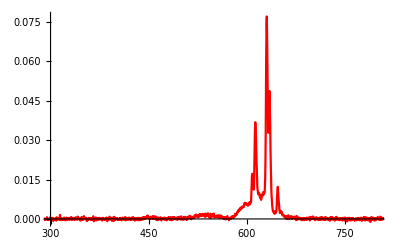

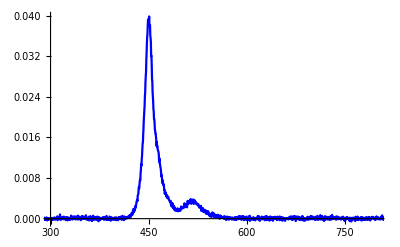

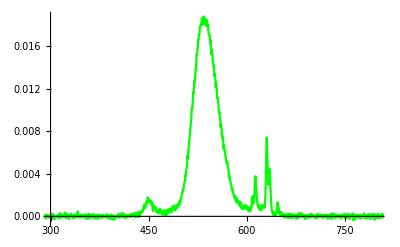

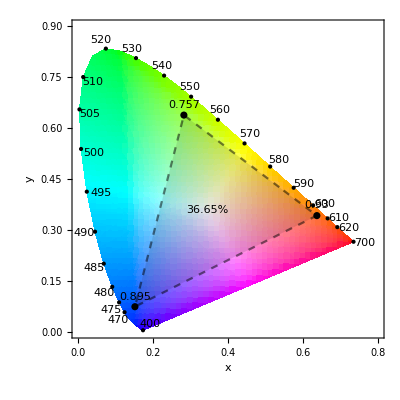

```mathematica
ip1150Red   = Import[dirstring<>"Data\\ip11_50\\ip11_50_red.csv"];
ip1150Blue = Import[dirstring<>"Data\\ip11_50\\ip11_50_blue.csv"];
ip1150Green= Import[dirstring<>"Data\\ip11_50\\ip11_50_green.csv"];
ip1150Back  = Import[dirstring<>"Data\\ip11_50\\ip11_50_back.csv"];
dataout[ip1150Red, ip1150Blue, ip1150Green, ip1150Back]
```

## IPhone 11 [100 % Brightness] :

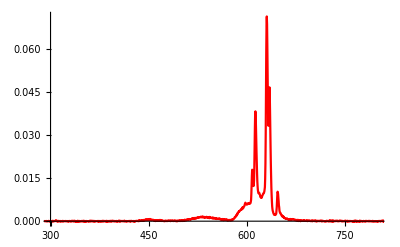

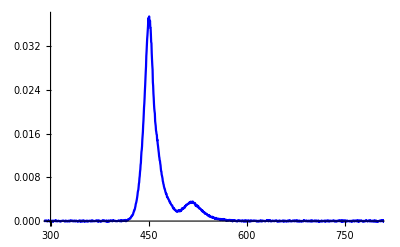

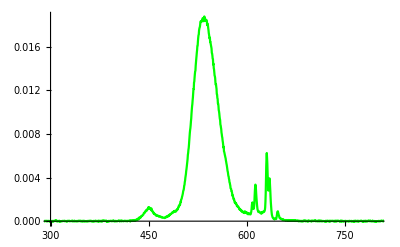

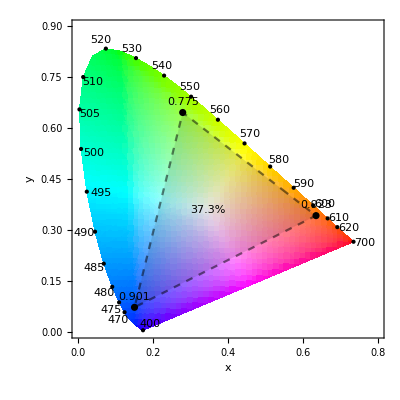

```mathematica
ip11hbRed   = Import[dirstring<>"Data\\ip11_highbright\\ip11_hb_red.csv"];
ip11hbBlue = Import[dirstring<>"Data\\ip11_highbright\\ip11_hb_blue.csv"];
ip11hbGreen= Import[dirstring<>"Data\\ip11_highbright\\ip11_hb_green.csv"];
ip11hbBack  = Import[dirstring<>"Data\\ip11_highbright\\ip11_hb_back.csv"];
dataout[ip11hbRed, ip11hbBlue, ip11hbGreen, ip11hbBack]
```

## IPhone 11 [Low Brightness] :

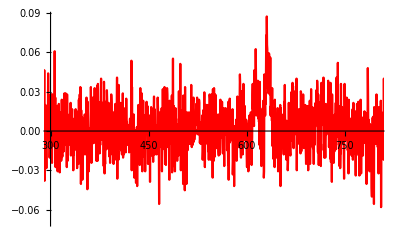

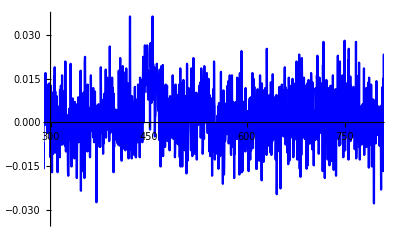

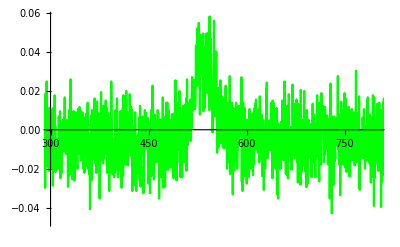

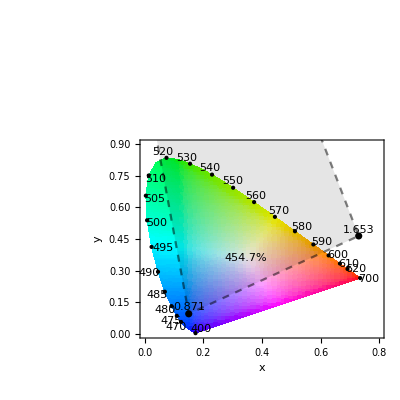

```mathematica
ip11lbRed   = Import[dirstring<>"Data\\ip11_lowbright\\ip11_lb_red.csv"];
ip11lbBlue = Import[dirstring<>"Data\\ip11_lowbright\\ip11_lb_blue.csv"];
ip11lbGreen= Import[dirstring<>"Data\\ip11_lowbright\\ip11_lb_green.csv"];
ip11lbBack  = Import[dirstring<>"Data\\ip11_lowbright\\ip11_lb_back.csv"];

ip11lbRed[[;;,2]]=ip11lbRed[[;;,2]]-ip11lbBack[[;;,2]];
ip11lbBlue[[;;,2]]=ip11lbBlue[[;;,2]]-ip11lbBack[[;;,2]];
ip11lbGreen[[;;,2]]=ip11lbGreen[[;;,2]]-ip11lbBack[[;;,2]];

ip11lbRed= normalize[ip11lbRed];
ip11lbGreen=normalize[ip11lbGreen];
ip11lbBlue=normalize[ip11lbBlue];

If[ip11lbRed[[;;,2]]<0, ip11lbRed[[;;,2]]=0,ip11lbRed[[;;,2]]=ip11lbRed[[;;,2]]];
If[ip11lbBlue[[;;,2]]<0,ip11lbBlue[[;;,2]]=0,ip11lbBlue[[;;,2]]=ip11lbBlue[[;;,2]]];
If[ip11lbGreen[[;;,2]]<0, ip11lbGreen[[;;,2]]=0,ip11lbGreen[[;;,2]]=ip11lbGreen[[;;,2]]];

ip11lbRedcord= colorcords[ip11lbRed];
ip11lbBluecord = colorcords[ip11lbBlue];
ip11lbGreencord= colorcords[ip11lbGreen];

ip11lbtri = ConvexHullMesh[{ip11lbRedcord,ip11lbBluecord,ip11lbGreencord}];
ip11lbarea =Area[ip11lbtri];

ip11lbcover = PercentForm[Round[ip11lbarea/purearea,0.0001]];

ip11lbrp= purity[ip11lbRedcord];
ip11lbbp= purity[ip11lbBluecord];
ip11lbgp= purity[ip11lbGreencord];

ip11lblabelr = Text[Round[ip11lbrp,0.001],{ip11lbRedcord[[1]],ip11lbRedcord[[2]]+0.03}];
ip11lblabelb = Text[Round[ip11lbbp,0.001],{ip11lbBluecord[[1]],ip11lbBluecord[[2]]+0.03}];
ip11lblabelg = Text[Round[ip11lbgp,0.001],{ip11lbGreencord[[1]],ip11lbGreencord[[2]]+0.03}];
ip11lblabela = Text[ip11lbcover, {0.34567,0.3585}];

ip11lbrplot = ListLinePlot[{ip11lbRed}, PlotRange ->{{300,800},All}, PlotStyle->{Red}];ip11lbbplot = ListLinePlot[{ip11lbBlue}, PlotRange->{{300, 800}, All},PlotStyle->{Blue}];
ip11lbgplot =  ListLinePlot[{ip11lbGreen},PlotRange ->{{300,800},All}, PlotStyle->{Green}];

ip11lbdataplot = ListPlot[{ip11lbRedcord,ip11lbBluecord,ip11lbGreencord}, PlotRange->{{0,1},{0,1}},PlotStyle->{Black}];
ip11lbtriplot = RegionPlot[ip11lbtri, BoundaryStyle->{Black,Dashed, Opacity[0.5]}, PlotStyle->{Black,Opacity[0.1]}];

ip11lbplotf  = Show[ChromaticityPlot[Appearance->{"FilledVisibleSpectrum","Wavelengths"->True}],ip11lbtriplot,ip11lbdataplot,Graphics[{Black,{ip11lblabelr, ip11lblabelb,ip11lblabelg,ip11lblabela}}]];
CellPrint@ExpressionCell[#,"Output"]&/@{ip11lbrplot,ip11lbbplot,ip11lbgplot,ip11lbplotf};
```

## IPhone 11 [No Screen Protector] :

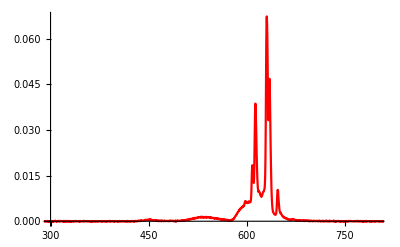

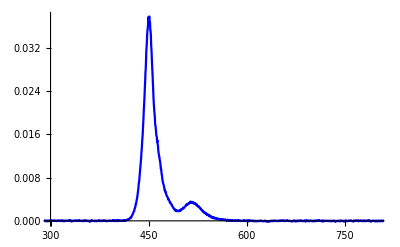

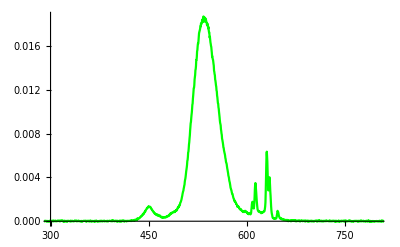

```mathematica
ip11npRed   = Import[dirstring<>"Data\\ip11_nopro\\ip11_np_red.csv"];
ip11npBlue = Import[dirstring<>"Data\\ip11_nopro\\ip11_np_blue.csv"];
ip11npGreen= Import[dirstring<>"Data\\ip11_nopro\\ip11_np_green.csv"];
ip11npBack  = Import[dirstring<>"Data\\ip11_nopro\\ip11_np_back.csv"];
dataout[ip11npRed, ip11npBlue, ip11npGreen, ip11npBack]
```